```mathematica
OutPutPath="ParralelD10";
SetDirectory[NotebookDirectory[]];
$P=2^31-1;
diffInvariants={mTsq,s23,s15,s45};
For[i=1,i<=4,i++,			
dhxbMatrices[diffInvariants[[i]]]=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/DEmatrix_d``",OutPutPath,diffInvariants[[i]]]]}]];
]
phasespacepoints=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/parameters",OutPutPath]]}]];
```

```mathematica
powerReconstruct[pars_,FitVecIn_]:=Module[{pars2,AnsatzPowersNumi,FitVec,AnsatzPowersDeno,MatNumiPart,onevc,parsCutOne,reconstructedFit,AnsatzPowersDenoOne,
fit,solrule,MatDenoPart,Solset,FinalMat,sol3,Ansatz,MaxPower},
	MaxPower=3;
AnsatzPowersNumi=FrobeniusSolve[{1,1},MaxPower];
	AnsatzPowersDeno=FrobeniusSolve[{1,1},MaxPower];
	pars2=pars/.{x_Integer:>{x,1}};
	(*MatNumiPart=Parallelize@Outer[m31ExpDot,pars2,AnsatzPowersNumi,1];*)

	MatNumiPart=Table[Table[Times@@PowerMod[pars2[[i]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}],{i,1,Length[pars2]}];
	(*Table[Times@@PowerMod[pars2[[1]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}]//Echo;*)
	
	FitVec=Expand[-FitVecIn,Modulus->$P];
	onevc=Table[{1},MaxPower+1];
	parsCutOne=MapThread[Join,{pars2,Transpose[{FitVec}]}];
	AnsatzPowersDenoOne=MapThread[Join,{AnsatzPowersDeno,onevc}];

	(*MatDenoPart=Parallelize@Outer[m31ExpDot,parsCutOne,AnsatzPowersDenoOne,1];*)
	
	MatDenoPart=Table[Table[Times@@PowerMod[parsCutOne[[i]],AnsatzPowersDenoOne[[j]],$P],{j,1,Length[AnsatzPowersDenoOne]}],{i,1,Length[parsCutOne]}];
	
	FinalMat=Expand[MapThread[Join,{MatNumiPart,MatDenoPart}],Modulus->$P];

	
	sol3=NullSpace[FinalMat,Modulus->$P];
	Ansatz=Sum[fac[n]t^n,{n,0,MaxPower}]/Sum[fac[n+MaxPower+1]t^n,{n,0,MaxPower}];
	Solset=Cases[Ansatz,fac[___],Infinity];
	solrule=Thread[Rule[Solset,sol3[[1]]]];
	fit=Together[Ansatz/.solrule]//ExpandDenominator//ExpandNumerator;
	Return[Expand[fit,Modulus->$P]]
]
```

```mathematica
LaunchKernels[20];
```

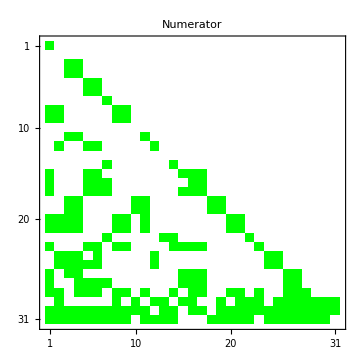
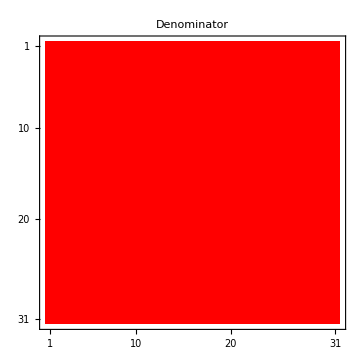
-Graphics- | -Graphics- |

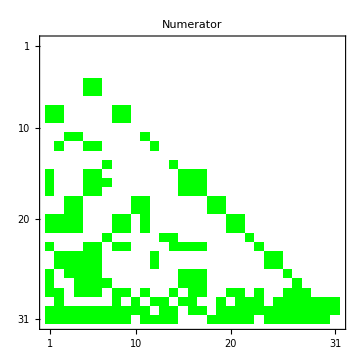
-Graphics- | -Graphics- |

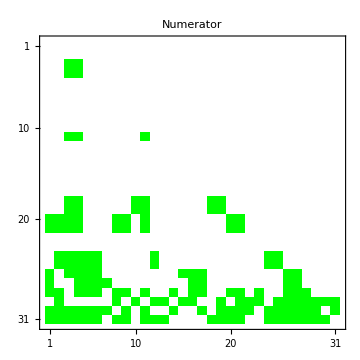
-Graphics- | -Graphics- |

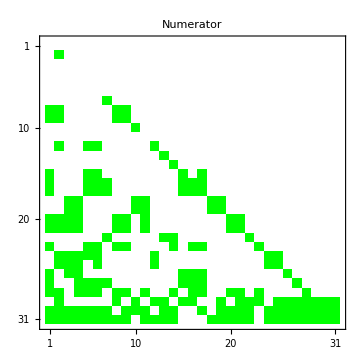
-Graphics- | -Graphics- |

```mathematica
colors={-1->White,0->Red,1->Green,2->Blue,3->Yellow,4->Orange,5->RGBColor["#e09f7d"],6->RGBColor["#EF5D60"],7->RGBColor["#EC4067"],8->RGBColor["#A01A7D"],9->RGBColor["#703399"],10->RGBColor["#0B050F"]};
CutsA=1;
CutsB=31;
For[i=1,i<=4,i++,
MatReco[diffInvariants[[i]]]=ParallelTable[Expand[powerReconstruct[phasespacepoints[[All,1]],dhxbMatrices[diffInvariants[[i]]][[All,pos]]]/.{t->4-2ϵ},Modulus->$P],{pos,1,Length[dhxbMatrices[s12][[1]]]}];
NumiPowers=Exponent[Numerator[MatReco[diffInvariants[[i]]]],ϵ]/.{-Infinity->-1};
DenoPowers=Exponent[Denominator[MatReco[diffInvariants[[i]]]],ϵ];
NumiPowersMat=NumiPowers//Normal;
DenoPowersMat=DenoPowers//Normal;
P1=MatrixPlot[ArrayReshape[NumiPowersMat,{31,31}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Numerator",ImageSize->Medium];
P2=MatrixPlot[ArrayReshape[DenoPowersMat,{31,31}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Denominator",ImageSize->Medium];
L1=SwatchLegend[Values@colors[[2;;]],Keys@colors[[2;;]],LegendFunction->"Frame",LegendLayout->"Column",LegendLabel->diffInvariants[[i]]];
Print[Grid[{{P1,P2,L1}}]];
]
```

```mathematica
ArrayReshape[MatReco[diffInvariants[[3]]],{31,31}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1771062723 ϵ | 165072518 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 845393624 ϵ | 1817338611 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1936135241 ϵ | 82536259 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 828484766 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1242928657 ϵ | 452277495 ϵ | 0 | 0 | 0 | 0 | 0 | 790651162 ϵ | 1581302324 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 1009416408 ϵ | 1581302324 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 972994721 ϵ | 587244463 ϵ | 0 | 0 | 0 | 0 | 0 | 633359035 ϵ | 1604688721 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 1698543969 ϵ | 606427998 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2142906925 ϵ | 311838148 ϵ | 863709368 ϵ | 73382815 ϵ | 0 | 0 | 0 | 566181323 ϵ | 1028781886 ϵ | 0 | 1613727226 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1900393785 ϵ | 1835645499 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1165335482 ϵ | 366374634 ϵ | 1727418736 ϵ | 348259835 ϵ | 0 | 0 | 0 | 897879356 ϵ | 2057563772 ϵ | 0 | 123031784 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1594574129 ϵ | 1120818941 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1642775443 ϵ | 1164956902 ϵ | 2141135860 ϵ | 1318998881 ϵ | 1985595366 ϵ | 0 | 0 | 0 | 0 | 0 | 566181323 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1065558493 ϵ | 504708204 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 880765577 ϵ | 1455475327 ϵ | 1860128772 ϵ | 490514115 ϵ | 1461843801 ϵ | 0 | 0 | 0 | 0 | 0 | 897879356 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 385952493 ϵ | 606427998 ϵ | 0 | 0 | 0 | 0 | 0 | 0
1583296470 ϵ | 0 | 1584126158 ϵ | 1469773363 ϵ | 490514115 ϵ | 1733241264 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1015121001 ϵ | 1581302324 ϵ | 128650831 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9854201 ϵ | 1982411129 ϵ | 0 | 0 | 0 | 0
1197546212 ϵ | 0 | 0 | 2033130852 ϵ | 128650831 ϵ | 1371377980 ϵ | 128650831 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 448939678 ϵ | 128650831 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1513438429 ϵ | 1780916924 ϵ | 0 | 0 | 0 | 0
507181984 ϵ | 1642775443 ϵ | 0 | 1390421341 ϵ | 128650831 ϵ | 1642775443 ϵ | 0 | 1132362646 ϵ | 2018832816 ϵ | 0 | 1266718070 ϵ | 0 | 0 | 128650831 ϵ | 0 | 1581302324 ϵ | 128650831 ϵ | 0 | 0 | 880765577 ϵ | 669780722 ϵ | 0 | 1132362646 ϵ | 0 | 0 | 1936135241 ϵ | 1982411129 ϵ | 1785620363 ϵ | 0 | 0 | 0
0 | 1761531154 ϵ | 0 | 0 | 0 | 0 | 0 | 1015121001 ϵ | 0 | 880765577 ϵ | 0 | 448939678 ϵ | 2018832816 ϵ | 0 | 566181323 ϵ | 1698543969 ϵ | 0 | 0 | 1744495237 ϵ | 0 | 1174488926 ϵ | 1015121001 ϵ | 1015121001 ϵ | 0 | 201494205 ϵ | 972994721 ϵ | 972994721 ϵ | 1785620363 ϵ | 1744495237 ϵ | 1015121001 ϵ | 2018832816 ϵ
1613116098 ϵ | 1132362646 ϵ | 566181323 ϵ | 566181323 ϵ | 1698543969 ϵ | 961506904 ϵ | 566181323 ϵ | 0 | 1015121001 ϵ | 0 | 1698543969 ϵ | 0 | 0 | 1132362646 ϵ | 0 | 0 | 117241645 ϵ | 0 | 117241645 ϵ | 448939678 ϵ | 224469839 ϵ | 2018832816 ϵ | 0 | 448939678 ϵ | 1805772163 ϵ | 566181323 ϵ | 566181323 ϵ | 1132362646 ϵ | 1132362646 ϵ | 0 | 1015121001 ϵ
1564815906 ϵ | 64219225 ϵ | 1428284234 ϵ | 1144036446 ϵ | 828484766 ϵ | 342819923 ϵ | 0 | 1698543969 ϵ | 1118701761 ϵ | 0 | 1000377903 ϵ | 1698543969 ϵ | 2018832816 ϵ | 0 | 0 | 0 | 0 | 1249604291 ϵ | 1543001032 ϵ | 276454759 ϵ | 513332353 ϵ | 0 | 0 | 880765577 ϵ | 871274927 ϵ | 972994721 ϵ | 972994721 ϵ | 1785620363 ϵ | 1945989442 ϵ | 1015121001 ϵ | 0)